```mathematica
(* Michael Barile 
  STAT 786
  HW #2, part 2 *)

L=101;
M=101;

uvecHalfSec = Import["/Users/michaelbarile/MathematicaFolder/uvecHalfSec.dat","list"];
```

```mathematica
uvec2Sec = Import["/Users/michaelbarile/MathematicaFolder/uvec2Sec.dat","list"];
```

```mathematica
uvec5Sec = Import["/Users/michaelbarile/MathematicaFolder/uvec5Sec.dat","list"];
```

```mathematica
pointsHalfSec = Import["/Users/michaelbarile/MathematicaFolder/pointsHalfSec.dat","Table"];
```

```mathematica
points2Sec = Import["/Users/michaelbarile/MathematicaFolder/points2Sec.dat","Table"];
```

```mathematica
points5Sec = Import["/Users/michaelbarile/MathematicaFolder/points5Sec.dat","Table"];
```

```mathematica
uvec = Import["/Users/michaelbarile/MathematicaFolder/uvec.dat","list"];
```

-Graphics3D-

-Graphics3D-

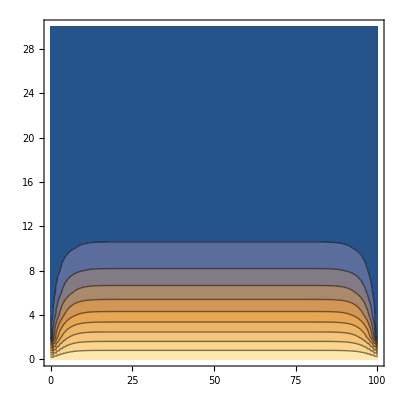

```mathematica
xvec={};

For[i=0,i≤100,++i,
AppendTo[xvec,i]
];

yvec={};
For[j=0,j≤15,++j,
AppendTo[yvec,2*j]
];

xyPoints={};
For[i=1,i≤Length[xvec],++i,
For[j=1,j≤Length[yvec],++j,
AppendTo[xyPoints,{xvec[[i]],yvec[[j]]}]
];
];
partition = Partition[uvecHalfSec,101];
reducedVec={};
irow={};
For[i=1,i≤101,++i,
For[j=1,j≤Length[yvec],++j,
AppendTo[reducedVec,partition[[i]][[j]]]
];
irow={};
];
For[i=1,i≤Length[reducedVec],++i,
AppendTo[xyPoints[[i]],reducedVec[[i]]]
];



ListPointPlot3D[pointsHalfSec,PlotRange->{Full,Full,Full}] 
ListPlot3D[pointsHalfSec,PlotRange->{Full,Full,Full},MeshFunctions->{#3&}] 
ListContourPlot[xyPoints]

(***************************** plots at t = 0.5 seconds ***************************)
```

-Graphics3D-

-Graphics3D-

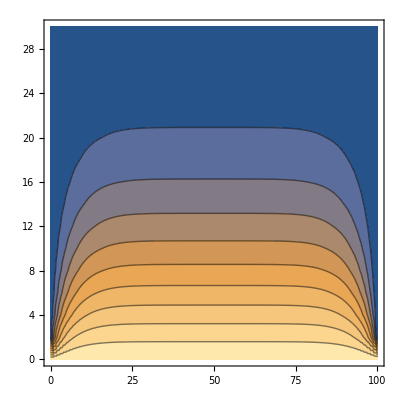

```mathematica
xvec={};

For[i=0,i≤100,++i,
AppendTo[xvec,i]
];

yvec={};
For[j=0,j≤15,++j,
AppendTo[yvec,2*j]
];

xyPoints={};
For[i=1,i≤Length[xvec],++i,
For[j=1,j≤Length[yvec],++j,
AppendTo[xyPoints,{xvec[[i]],yvec[[j]]}]
];
];
partition = Partition[uvec2Sec,101];
reducedVec={};
irow={};
For[i=1,i≤101,++i,
For[j=1,j≤Length[yvec],++j,
AppendTo[reducedVec,partition[[i]][[j]]]
];
irow={};
];
For[i=1,i≤Length[reducedVec],++i,
AppendTo[xyPoints[[i]],reducedVec[[i]]]
];

ListPointPlot3D[points2Sec,PlotRange->{Full,Full,Full}] 
ListPlot3D[points2Sec,PlotRange->{Full,Full,Full},MeshFunctions->{#3&}] 
ListContourPlot[xyPoints]

(***************************** plots at t = 2 seconds ***************************)
```

-Graphics3D-

-Graphics3D-

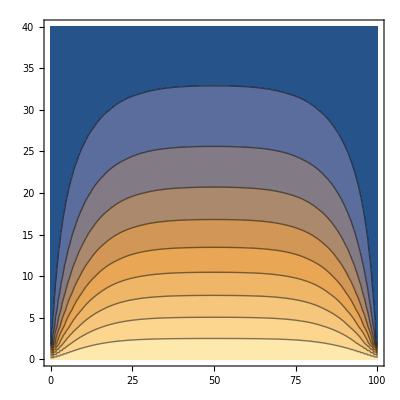

```mathematica
xvec={};

For[i=0,i≤100,++i,
AppendTo[xvec,i]
];

yvec={};
For[j=0,j≤20,++j,
AppendTo[yvec,2*j]
];

xyPoints={};
For[i=1,i≤Length[xvec],++i,
For[j=1,j≤Length[yvec],++j,
AppendTo[xyPoints,{xvec[[i]],yvec[[j]]}]
];
];
partition = Partition[uvec5Sec,101];
reducedVec={};
irow={};
For[i=1,i≤101,++i,
For[j=1,j≤Length[yvec],++j,
AppendTo[reducedVec,partition[[i]][[j]]]
];
irow={};
];
For[i=1,i≤Length[reducedVec],++i,
AppendTo[xyPoints[[i]],reducedVec[[i]]]
];
ListPointPlot3D[points5Sec,PlotRange->{Full,Full,Full}] 
ListPlot3D[points5Sec,PlotRange->{Full,Full,Full},MeshFunctions->{#3&}] 
ListContourPlot[xyPoints]

(***************************** plots at t = 5 seconds ***************************)
```